```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=5
(*Distance between quark and anti-quark*)
r:=1
(*Integration Bounds*)
l:=50
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Define instanton solutions
Areg[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)
Aanti[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)*)
```

```mathematica
(*Test Values*)
θtest={θ3->1.,θ1->0.,θ2->1.,θ4->1.,θ5->1.,θ6->0.};
ypoint={1.,1.,0.,0.};
rottest=IdentityMatrix[4];
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
(*2 unit vectors will specify a plane and its dual to be rotated around*)
(*u1={Sin[θ1]Sin[θ2]Sin[θ3],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}
u2={Sin[θ4]Sin[θ5]Sin[θ6],Sin[θ4]Sin[θ5]Cos[θ6],Sin[θ4]Cos[θ5],Cos[θ6]}
u1.u2/.θtest
A=Sum[LeviCivitaTensor[4][[i]][[j]]u1[[i]]u2[[j]],{i,1,4},{j,1,4}]
AntisymmetricMatrixQ[A]
th1=Eigenvalues[A][[2]]/I;
th2=Eigenvalues[A][[4]]/I;
Eigenvalues[A]/.θtest
A1=1/(th1(th2^2-th1^2))(th2^2A+A.A.A)
A2=1/(th2(th1^2-th2^2))(th1^2A+A.A.A)*)
```

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arat[y_]:=Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]
Arot[y_,rot_]:=(rot).Arat[(rot).y] (* here is the rotation acts on a molecule *)
Dimensions[Arot[ypoint,rottest]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
```

```mathematica
(*SU(3) rotation vector at various points*)
RotV[a_]:=a[[4]]/Sqrt[a[[4]].a[[4]]]
RotV[Arot[ypoint+{0,0,0,(1-1/2)L/n}]]/.θtest
RotV[Arot[ypoint+{0,0,0,(2-1/2)L/n}]]/.θtest
Plot[RotV[Arot[ypoint+{0,0,0,(i-1/2)L/n}]][[1]]/.θtest,{i,1,10}]
```

Part::partw: Part 4 of Arot[{1.,1.,0.,0.5}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(Arot[{1.,1.,0.,0.5}]⟦4⟧)/(√(Arot[{1.,1.,0.,0.5}]⟦4⟧.Arot[{1.,1.,0.,0.5}]⟦4⟧))

Part::partw: Part 4 of Arot[{1.,1.,0.,1.5}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(Arot[{1.,1.,0.,1.5}]⟦4⟧)/(√(Arot[{1.,1.,0.,1.5}]⟦4⟧.Arot[{1.,1.,0.,1.5}]⟦4⟧))

Part::partw: Part 4 of Arot[{1.,1.,0.,0.500184}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
(*Table of wilson lines along L*)
WList[y_,rot_]:=Table[W2[Arot[y+{0,0,0,(i-1/2)L/n},rot]],{i,1,n}]
WdList[y_,rot_]:=Table[Wd2[Arot[y+{0,0,0,(i-1/2)L/n},rot]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_,rot_]:=Dot@@WList[y,rot] (* applies the function to everything in the table *)
Wdapprox[y_,rot_]:=Dot@@WdList[y,rot]
```

```mathematica
(*The timing to compute a single point with all numerical inputs is 0.05 seconds.  Times 
10,000 this is 500 seconds or 8 minutes, which is pretty good.  If y is not part of the monte carlo, the timing is 27 seconds, which is not viable for more than 1 or 2 data points.*)
timing1=AbsoluteTiming[Wapprox[y]/.θtest]
```

{8.4×10^-6,Wapprox[y]}

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WApproxLower[y_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
WdApproxUpper[y_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WdApproxLower[y_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
```

```mathematica
Tr[Mexample.ConjugateTranspose[Mexample]]
```

Tr[Mexample.ConjugateTranspose[Mexample]]

```mathematica
Mexample // MatrixForm
```

Mexample

```mathematica
Imes[y_,rot_,rr_]:=1-1/2*Tr[Wapprox[y,rot].Wdapprox[y-{rr,0,0,0},rot]](* integrand *)
```

```mathematica
(*Obtaining random spherically distributed points.*)
RandSphere:=Module[{r,poi},r=2;
While[r>1,
poi=RandomReal[{-1,1},4];
r=Norm[poi]]; 
poi=poi/r;
poi ]
{RandSphere,RandSphere}
(*ListPlot[Table[randSphere,100],AspectRatio->1]*)
```

{{0.596395,-0.356955,0.647404,0.312673},{-0.217148,0.24626,-0.490653,0.807133}}

```mathematica
(*Random sampling of rotation matricies*)
RotR[a_]:=
{{a[[1]],-a[[2]],-a[[3]],-a[[4]]},
{a[[2]],a[[1]],-a[[4]],a[[3]]},
{a[[3]],a[[4]],a[[1]],-a[[2]]},
{a[[4]],-a[[3]],a[[2]],a[[1]]}};
RotL[p_]:={{p[[1]],-p[[2]],-p[[4]],-p[[3]]},
{p[[2]],p[[1]],p[[3]],-p[[4]]},
{p[[4]],-p[[3]],p[[1]],p[[2]]},
{p[[3]],p[[4]],-p[[2]],p[[1]]}};
Rot[a_,p_]:=RotL[a].RotR[p]
randRot:=Rot[RandSphere,RandSphere]
```

```mathematica
randY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*Under 0.1 Seconds!*)
AbsoluteTiming[Imes[randY,randRot,5]]
```

{0.0863678,0.00354143+0. ⅈ}

```mathematica
(*Number of test points for monte carlo*)
num=10000
```

10000

```mathematica
(*Error of Monte Carlo*)
randMes=Table[Imes[randY,randRot,5],num]; (* num is number of test points *)
1/num*Sum[randMes[[i]],{i,1,num}]
randMes=Table[Imes[randY,randRot,5],num];
1/num*Sum[randMes[[i]],{i,1,num}]
randMes=Table[Imes[randY,randRot,5],num];
1/num*Sum[randMes[[i]],{i,1,num}]
```

0.00294414+0. ⅈ

0.00252668+0. ⅈ

0.00275229+0. ⅈ

```mathematica
DistanceTablesMes=Table[Table[Imes[randY,randRot,5],num],{rr,0,100,10}]; (* num=10000 times in each and then 10 rr values *)
DistanceDataMes=Table[{rr,1/num*Sum[DistanceTablesMes[[rr,i]],{i,1,num}]},{rr,1,10}]
```

{{1,0.00262486+0. ⅈ},{2,0.00326236+0. ⅈ},{3,0.00286947+0. ⅈ},{4,0.00325757+0. ⅈ},{5,0.00270016+0. ⅈ},{6,0.00280537+0. ⅈ},{7,0.00281102+0. ⅈ},{8,0.0027558+0. ⅈ},{9,0.0029014+0. ⅈ},{10,0.00258293+0. ⅈ}}

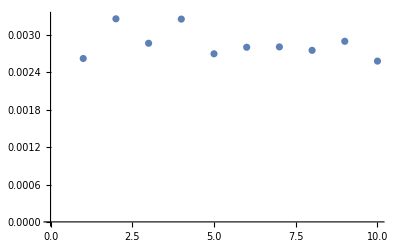

```mathematica
ListPlot[{{1,0.0026248611267067827+0. ⅈ},{2,0.0032623641572011317+0. ⅈ},{3,0.00286947385850002+0. ⅈ},{4,0.0032575689244120107+0. ⅈ},{5,0.002700156732538671+0. ⅈ},{6,0.002805373247498679+0. ⅈ},{7,0.0028110223686057885+0. ⅈ},{8,0.0027557987902220335+0. ⅈ},{9,0.002901396942899301+0. ⅈ},{10,0.002582932690244667+0. ⅈ}},PlotRange->{0.,.0033}]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arat[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arat[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arat[{y[1],y[2],y[3],0}][[mu]][[b]]Arat[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
B[y1_,y2_,y3_,t_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j]][[k]][[a]]/.{y[1]->y1,y[2]->y2,y[3]->y3,y[4]->t})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
```

```mathematica
B[ypoint[[1]],ypoint[[2]],ypoint[[3]],1][[1]]/.{θ3->1.,θ1->0,θ2->0}
```

{{0.0161029,0.121208-0.0326775 ⅈ},{0.121208+0.0326775 ⅈ,-0.0161029}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y1_,y2_,y3_,t1_,t2_]:=Sum[Tr[WApproxLower[{y1,y2,y3,0},t1].B[y1,y2,y3,t1][[i]].WApproxUpper[{y1,y2,y3,0},t1].WdApproxUpper[{y1-r,y2,y3,0},t2].B[y1,y2,y3,t1][[i]].WdApproxLower[{y1-r,y2,y3,0},t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[ImesBB[ypoint[[1]],ypoint[[2]],ypoint[[3]],1,1]/.{θ3->1.,θ1->0,θ2->0}]
```

{0.326356,0.0569468+0. ⅈ}

```mathematica
AngleDataMesBB=Table[{θ3,Sum[(L/n)^2*NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]ImesBB[y1,y2,y3,t1,t2],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2],{t1,1,n},{t2,1,n}]},{θ3,0,Pi,Pi/4}]
```

$Aborted

```mathematica
ListPlot[AngleDataMesBB]
```

```mathematica
(*SU(3) matrix for baryon*)
WapproxBar[y_]:=ArrayFlatten[{{Wapprox[y],0},{0,1}}]
```

```mathematica
Sum[LeviCivitaTensor[3][[b1]][[b2]][[b3]]LeviCivitaTensor[3][[c1]][[c2]][[c3]]w1[b1,c1]w2[b2,c2]KroneckerDelta[b3,c3],{b1,1,3},{b2,1,3},{b3,1,3},{c1,1,3},{c2,1,3},{c3,1,3}]
```

w1[2,2] w2[1,1]+w1[3,3] w2[1,1]-w1[2,1] w2[1,2]-w1[3,1] w2[1,3]-w1[1,2] w2[2,1]+w1[1,1] w2[2,2]+w1[3,3] w2[2,2]-w1[3,2] w2[2,3]-w1[1,3] w2[3,1]-w1[2,3] w2[3,2]+w1[1,1] w2[3,3]+w1[2,2] w2[3,3]

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rr_]:=(*1-1/6(WapproxBar[y][[2]][[2]]WapproxBar[y-{rr,0,0,0}][[1]][[1]]+
WapproxBar[y][[3]][[3]]WapproxBar[y-{rr,0,0,0}][[1]][[1]]-
WapproxBar[y][[2]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[2]]-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]-
WapproxBar[y][[1]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[1]]+
WapproxBar[y][[1]][[1]]WapproxBar[y-{rr,0,0,0}][[2]][[2]]+
WapproxBar[y][[3]][[3]]WapproxBar[y-{rr,0,0,0}][[2]][[2]]-
WapproxBar[y][[3]][[2]]WapproxBar[y-{rr,0,0,0}][[2]][[3]]-
WapproxBar[y][[3]][[1]]WapproxBar[y-{rr,0,0,0}][[1]][[3]]-
WapproxBar[y][[2]][[3]]WapproxBar[y-{rr,0,0,0}][[3]][[2]]+
WapproxBar[y][[1]][[1]]WapproxBar[y-{rr,0,0,0}][[3]][[3]]+
WapproxBar[y][[2]][[2]]WapproxBar[y-{rr,0,0,0}][[3]][[3]]
)*)1-1/6(LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[3]]+
LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[2]]+LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[1]]-
LeviCivitaTensor[3].WapproxBar[y][[1]].WapproxBar[y-{rr,0,0,0}][[3]].WapproxBar[y-{0,rr,0,0}][[2]]-
LeviCivitaTensor[3].WapproxBar[y][[2]].WapproxBar[y-{rr,0,0,0}][[1]].WapproxBar[y-{0,rr,0,0}][[3]]-LeviCivitaTensor[3].WapproxBar[y][[3]].WapproxBar[y-{rr,0,0,0}][[2]].WapproxBar[y-{0,rr,0,0}][[1]])
```

```mathematica
AbsoluteTiming[Ibar[{100,100,100,0},r]/.{θ3->1.,θ1->0,θ2->0}]
```

{26.6473,6.86381×10^-7+3.5293×10^-23 ⅈ}

```mathematica
AbsoluteTiming[Ibar2[ypoint]/.{θ3->1.,θ1->0,θ2->0}]
```

{280.352,1.-0.0825364 ⅈ}

```mathematica
AngleDataBar=Table[{θ3,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Ibar[{y1,y2,y3,0},r],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{θ3,0,Pi,Pi/20}]
```

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[π/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand ((-1+√5)^2 Ibar[{y1,y2,y3,0},1] Sin[θ2])/(32 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

NIntegrate::inumr: The integrand (Ibar[{y1,y2,y3,0},1] Sin[(3 π)/20]^2 Sin[θ2])/(2 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{-20,20},{-20,20},{-20,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0,0.},{π/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(2 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π/2,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(11 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(13 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(7 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(3 π)/4,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(4 π)/5,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(17 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(9 π)/10,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{(19 π)/20,NIntegrate[(Sin[θ3]^2 Sin[θ2] Ibar[{y1,y2,y3,0},r])/(2 π^2),{θ1,0,2 π},{θ2,0,π},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal→2]},{π,0.}}

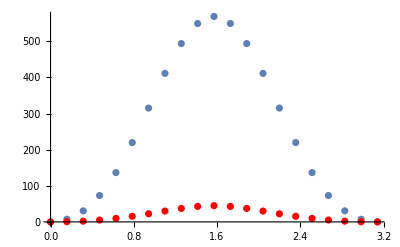

```mathematica
Show[ListPlot[AngleDataBar],ListPlot[AngleDataMes, PlotStyle->Red]]
```

```mathematica
DistanceDataBar=Table[{rr,NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]Sin[θ6]^2Sin[θ5]Ibar[{y1,y2,y3,0},rr],{θ1,0,2Pi},{θ2,0,Pi},{θ3,0,Pi},{θ4,0,2Pi},{θ5,0,Pi},{θ6,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,5,0.5}]
```

$Aborted

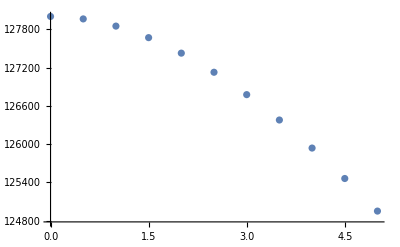

```mathematica
ListPlot[DistanceDataBar]
```

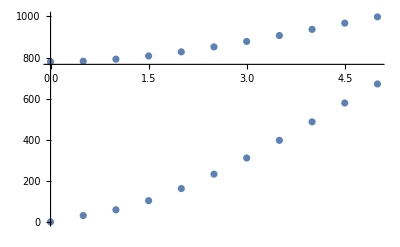

```mathematica
Show[ListPlot[{{0.,778.9835213308644},{0.5,782.3267046267691},{1.,792.152492607173},{1.5,807.7028960522447},{2.,827.7081944981895},{2.5,851.8575212904334},{3.,878.4555047811792},{3.5,907.1199034362559},{4.,937.2130977795467},{4.5,967.6137088101215},{5.,998.061197351786}}], ListPlot[{{0.,0.002512441216923788},{0.5,30.91367243239993},{1.,58.91338735249828},{1.5,103.40412743171798},{2.,162.2505756110101},{2.5,232.31559924567807},{3.,311.0906448660886},{3.5,396.9399695224351},{4.,486.9764667481333},{4.5,578.8795437770816},{5.,671.5149104549458}}],PlotStyle->Red,PlotRange->{0,1000}]
```

```mathematica
DistanceDataMes=
```

DistanceDataMes

$Aborted